{surface0.gpl,surface1.gpl,surface2.gpl,surface3.gpl,surface4.gpl,surface5.gpl,surface6.gpl,surface7.gpl,surface8.gpl,surface9.gpl,surface10.gpl}

/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion

{{50,10460.1},{51,10428.5},{52,10399.9},{53,10375.5},{54,10346},{55,10320.3},{56,10295.2},{57,10270.8},{58,10247.1},{59,10223.9},{60,10201.2}}

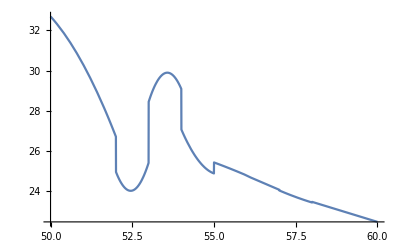

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion/gpls"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange -> All];
{plot1,plot2}
]
files= FileNames[];
(*Print[files]*)
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
ListAnimate[allPlots]
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
]
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion"]
Print[SolveForce["energysep.txt"]];
energysepfunc = Interpolation[SolveForce["energysep.txt"]];
forcefunction = energysepfunc';
Plot[-1*(forcefunction[x]), {x, 50, 60}, PlotRange->All]
```

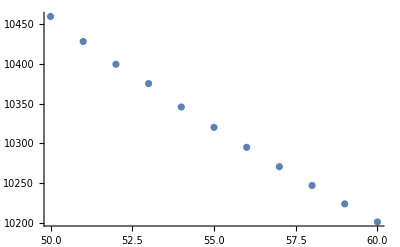

```mathematica
ListPlot[SolveForce["energysep.txt"], PlotRange->All]
```